# Moduł 1

## 1. Narysuj wykresy poniższych funkcji (w przypadku jedno- i dwuwymiarowym):

-> funkcja sferyczna

```mathematica
ClearAll["Global`*"];
```

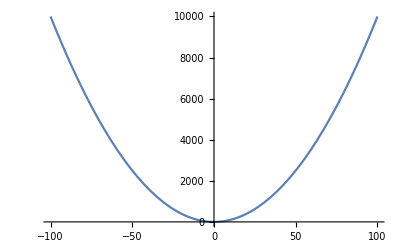

```mathematica
SphericFunction[x_]:=x^2;
Plot[SphericFunction[x],{x,-100,100}]
```

```mathematica
SphericFunction2D[x_,y_]:=x^2+y^2;
Plot3D[SphericFunction2D[x,y],{x,-100,100},{y,-100,100}]
```

-Graphics3D-

-> funkcja Rastrigina

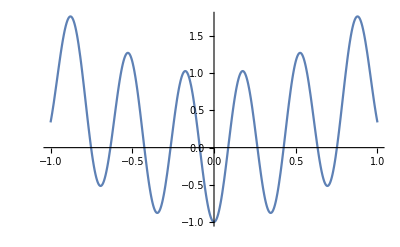

```mathematica
RastriginFunction[x_]:=x^2-Cos[18*x];
Plot[RastriginFunction[x],{x,-1,1}]
```

```mathematica
RastriginFunction2D[x_,y_]:=x^2-Cos[18*x]+y^2-Cos[18*y];
Plot3D[RastriginFunction2D[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

-> funkcja Ackley’a

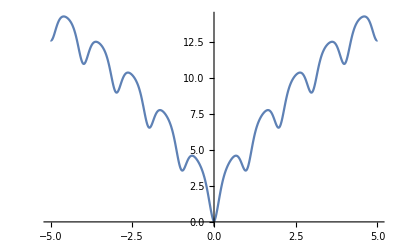

```mathematica
AckleyFunction[x_]:=-20*Exp[-0.2*√(x^2)]-Exp[Cos[2*Pi*x]]+20+ⅇ;
Plot[AckleyFunction[x],{x,-5,5}]
```

```mathematica
AckleyFunction2D[x_,y_]:=-20*Exp[-0.2*√(1/2*(x^2+y^2))]-Exp[1/2*(Cos[2*Pi*x]+Cos[2*Pi*y])]+20+ⅇ;
Plot3D[AckleyFunction2D[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

->dolina Rosenbrocka

```mathematica
RosenbrockFunction2D[x_,y_]:=(1-x)^2+100(y-x^2)^2;
Plot3D[RosenbrockFunction2D[x,y],{x,-5,5},{y,-10,10}]
```

-Graphics3D-

-> funkcja Himmelblaua

```mathematica
HimmelblauFunction2D[x_,y_]:=(x^2+y-11)^2+(x+y^2-7)^2;
Plot3D[RosenbrockFunction2D[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

->funkcja Beale’a

```mathematica
BealeFunction2D[x_,y_]:=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x y^3)^2;
Plot3D[BealeFunction2D[x,y],{x,-4.5,4.5},{y,-4.5,4.5}]
```

-Graphics3D-

## 2. Napisz program pml_basic, który szuka minimum funkcji testowej, stosując prostą metodę losową (PML).

```mathematica
PML[function_,Xdomain_,Ydomain_,iterations_,numberOfPoints_,ep_,x0_]:=Module[{randomPoints={},bestPoint,bestValue,sum,actualPoint,actualValue,bestPointOverall={},bestValueOverall=function[x0⟦1⟧,x0⟦2⟧],results={},bestValues={},means={},currentPoint=x0,e=ep,locations={}},

(*pętla, w której wykonujemy cały algorytm prostej metody losowej*)
(* kryterium zatrzymania to kryterium kosztowe - maksymalna ilość iteracji *)
For[i=1,i≤iterations,i++,
(* pseudolosowe liczby w sąsiedztwie bieżącego punktu (obszar kwadratu)*)
randomPoints=RandomPoint[Rectangle[currentPoint-e,currentPoint+e],numberOfPoints];

(* przypisanie do najlepszego punktu pierwszego  z pseudowylosowanych punktów *)
bestPoint=randomPoints⟦1⟧;
bestValue=function[bestPoint⟦1⟧,bestPoint⟦2⟧];
sum=0;

(* obliczanie wartości dla każdego punktu *)
For[j=1,j≤numberOfPoints,j++,
actualPoint={randomPoints⟦j,1⟧,randomPoints⟦j,2⟧};
actualValue=function[actualPoint⟦1⟧,actualPoint⟦2⟧];
sum=sum+actualValue;
(* przypisanie nowych wartości (punktu i wartości) jeśli wartość jest większa dla obecnego punktu*)
If[actualValue<bestValue,bestPoint=actualPoint;bestValue=actualValue;];
];

(*dodanie do listy wszystkich średnich wyniku średniego w danej iteracji*)
AppendTo[means,sum/numberOfPoints];

(* przypisanie do bieżącego punktu najlepszego punktu w danej iteracji *)
currentPoint=bestPoint;
AppendTo[locations,currentPoint];

(* sprawdzenie czy najlepsza wartość w danej iteracji jest najlepsza ze wszystkich dotychczasowych wyników - jeśli tak, przypisanie najlepszego punktu i wartości do najlepszych ogólnie *)
If[bestValue<bestValueOverall,bestPointOverall=bestPoint;bestValueOverall=bestValue;];

(* dodanie najlepszego wyniku do listy wszystkich wyników końcowych *)
AppendTo[results,bestValueOverall];
];

Return[{bestPointOverall,bestValueOverall,results,means,locations}];
];
```

## 3. Napisz program dzialanieHeurystyki prezentujący działanie powyższej (w praktyce dowolnej) metody optymalizacyjnej.

```mathematica
dzialanieHeurystyki[function_,domainX_,domainY_,iterations_,numberOfPoints_,e_,x0_]:=Module[{bestPointOverall,bestValueOverall,results,means,locations,animation,optimum,resultsPlot,meansPlot},{bestPointOverall,bestValueOverall,results,means,locations}=PML[function,domainX,domainY,iterations,numberOfPoints,e,x0];

(* znalezione optimum\small{x_{max}} oraz wartość funkcji celu w tym punkcie*)
optimum=StringJoin["fMin(",ToString[bestPointOverall⟦1⟧],", ",ToString[bestPointOverall⟦2⟧],")=",ToString[bestValueOverall]];

(* przebieg wartości optymalnej w kolejnych iteracjach\small{x_{best,i}} *)
resultsPlot=ListPlot[results,PlotStyle->{Purple},AxesLabel->{"ilość iteracji","wartość"}, PlotLabel->"przebieg Φ(xBest)",ImageSize->400 ];

(* przebieg wartości średniej (w populacji) w kolejnych iteracjach\small{x_{av,i}} *)
meansPlot=ListLinePlot[means,PlotStyle->{Purple,Thick},AxesLabel->{"ilość iteracji","średnia wartość"},PlotLabel->"przebieg Φ średnie w iteracji" ,ImageSize->400];
(* ruch punktu\small{x_{best,i}} na płaszczyźnie (dla problemów 2D) *)
animation=Animate[Module[{currentLocation=locations⟦j⟧,from=locations⟦1;;j-1⟧,to=locations[[2;;j]]},DensityPlot[function[x,y],{x,domainX⟦1⟧,domainX⟦2⟧},{y,domainY⟦1⟧,domainY⟦2⟧},Epilog->{Red,PointSize[Large],Point[currentLocation],Thick,Line[Transpose[{from,to}]],Thin,Line[Transpose[{locations⟦1;;j-1⟧,locations⟦2;;j⟧}]]}]],{j,1,iterations,1}];
Print[Grid[{{optimum,resultsPlot},{meansPlot,animation}},Frame->All,Alignment->Left,ItemSize->{36,25}]];
]
```

->funkcja sferyczna

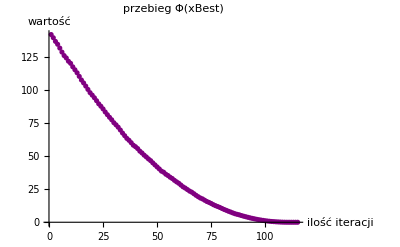
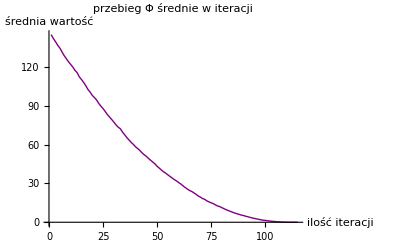
fMin(0.00876271, 0.00477754)=0.00009961 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[SphericFunction2D,{-10,10},{-10,10},115,30,0.1,{8,-9}];
```

Wartość optymalna funkcji wynosi 0, więc

## -> funkcja Rastrigina

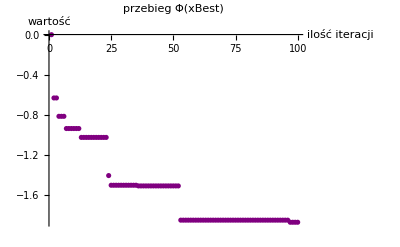
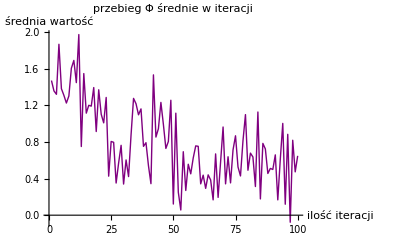
fMin(0.0056631, -0.353045)=-1.86757 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[RastriginFunction2D,{-1,1},{-1,1},100,20,0.25,{0.9, 0.7}];
```

PML sprawdza się dla funkcji testowej Rastrigina na większym obszarze sąsiedztwa lub e=0.1, gdy liczba losowanych punktów wynosi 2 lub 3, gdyż inaczej zatrzymuje się w minimum lokalnym.

## -> funkcja Ackley’a

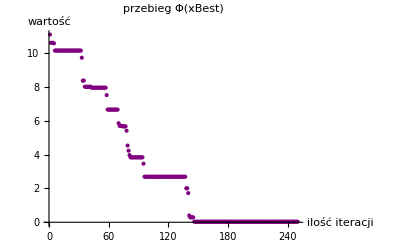
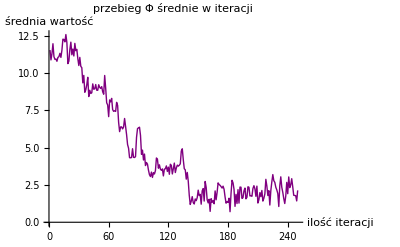
fMin(0.00920506, -0.00437432)=0.0315898 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[AckleyFunction2D,{-5,5},{-5,5},250,3,0.3,{3,3.7}];
```

Tu podobnie jak w poprzedniej funkcji, najlepiej sprawdza się większy zakres sąsiedztwa oraz mniejsza ilość losowych punktów, gdyż inaczej zatrzymuje się w minimum lokalnym.

## ->dolina Rosenbrocka

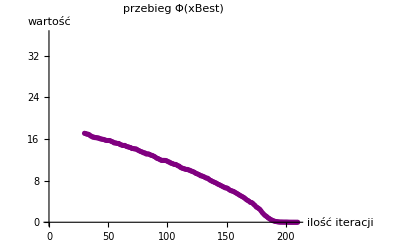
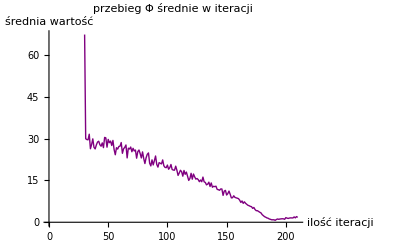
fMin(0.989174, 0.977172)=0.000284531 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[RosenbrockFunction2D,{-10,10},{-10,10},210,70,0.1,{-6,8}];
```

Funkcja sprawdza się dla dużej ilości punktów losowych i mniejszej ilości iteracji lub na odwrót.

## -> funkcja Himmelblaua

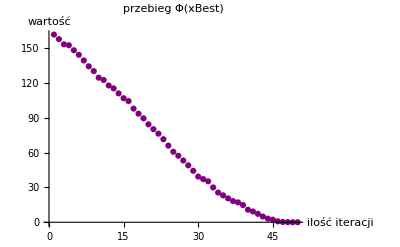
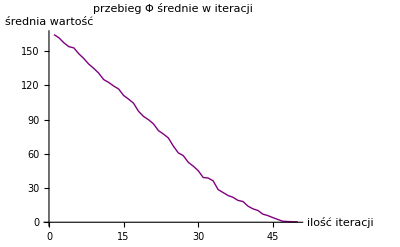
fMin(-2.76975, 3.1416)=0.0449019 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[HimmelblauFunction2D,{-5,5},{-5,5},50,10,0.1,{-1,0}];
```

Funkcja bez problemów znajduje jedno z czterech minimum.

## ->funkcja Beale’a

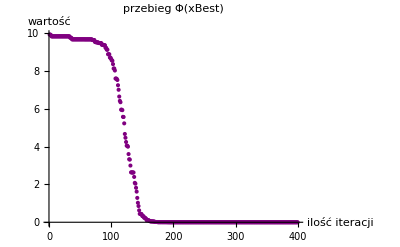
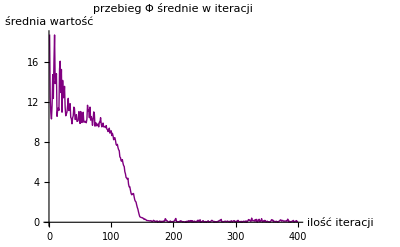
fMin(2.98883, 0.497885)=0.0000303918 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[BealeFunction2D,{-5,5},{-5,5},400,3,0.1,{0,-3}];
```

Algorytmowi zazwyczaj udaje się wyjść z tego minimum lokalnego.

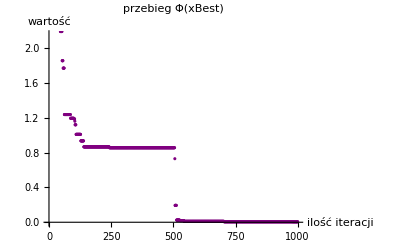
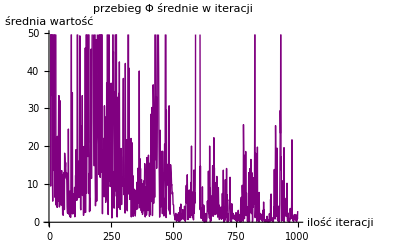
fMin(2.84063, 0.451512)=0.00560428 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[BealeFunction2D,{-5,5},{-5,5},1000,2,0.4,{-1,3}];
```

W przypadku tego punktu początkowego algorytm czasem wydostaje się z minimum lokalnego i znajduje globalne, przy niskiej ilości losowanych liczb -> 2 lub 3, większym zakresie sąsiedztwa jak i dużej ilości iteracji.

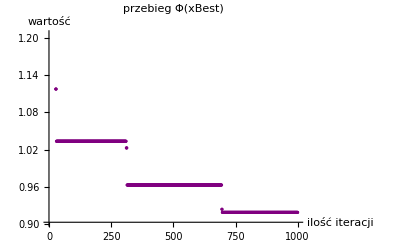
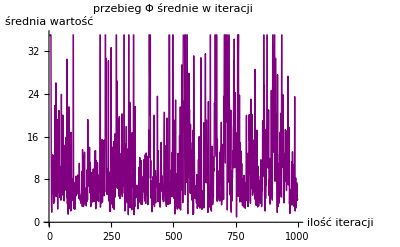
fMin(-3.01245, 1.27)=0.918702 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki[BealeFunction2D,{-5,5},{-5,5},1000,3,0.4,{-2,0}];
```

W przypadku tego punktu początkowego, algorytm czasem bez problemu znajduje minimum globalne, a czasem wpada w lokalne, więc zostaje większa ilość iteracji jak i obszaru sąsiedztwa oraz mała ilość losowych punktów, gdyż wtedy może się uda znaleźć algorytmowi minimum globalne.

## Prosta metoda losowa bardzo dobrze radzi sobie dla większości użytych funkcji testowych, trzeba było tylko dostosować odpowiednie parametry. Jednak w przypadku funkcji Beale’a często nie radzi sobie i nie wychodzi z minimum lokalnego (zależy to też od tego, jaki punkt początkowy weźmiemy).